# Experiment 20 - The Geiger-Müller Detector

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
(* We export the data from the lab notebook for analysis in CurveFit. *)
SetDirectory[NotebookDirectory[]];
v0vp={{"S V0(V)","Vp(V)"},{ 800,{2.96,2.94,2.98}},{790,{2.48,2.42,2.46}},{780,{1.88,1.88,1.82}},{770,{1.34,1.38,1.38}},{760,{0.92,0.912,0.928}},{750,{0.480,0.484,0.480}},{740,{0.119,0.120,0.122}},{738,{0.0736,0.0704,0.0712}},{800,{3.02,2.96,3.00}},{825,{3.92,3.96,3.92}},{850,{4.76,4.72,4.72}},{875,{5.68,5.52,5.68}},{900,{6.64,6.52,6.64}},{812,{3.46,3.46,3.40}},{837,{4.28,4.24,4.32}},{862,{5.08,5.16,5.16}},{887,{6.08,6.08,5.96}}};

(* Match first element of list to every element of corresponding sublist to split data into tuples. *)
match[list_]:=If[StringTake[ToString[list[[1]]],1]=="S",{list},Table[{list[[1]],list[[2]][[i]]},{i,1,Length[list[[2]]]}]];
v0vpDat=Flatten[Table[match[v0vp[[i]]],{i,1,Length[v0vp]}],1];
td={{"S V0(V)","td(us)"},{780,83},{800,80},{820,78},{840,74},{880,70},{920,66},{950,68}};

Export["v0vp.dat",v0vpDat];
Export["td.dat",td];
```

## Determining V_Th

The threshold voltage V_Th is the smallest bias voltage for which Townsend cascades occur, i.e. the smallest V_0 for which pulses are detected. Therefore, our determination of V_0 will be carried out by performing a (linear) fit of V_0 against V_p and observing the y-intercept of the fit, essentially extrapolating to the point where the pulses just vanish.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 20/v0vp.dat

File comment header:

V0(V)	Vp(V)

LoadFile::sorted: Data sorted in increasing x order.

Read 51 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
LinearFit[]
```

n = 51

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
734.034 | b= 
24.4735 | 
σ_a= 
1.1047 | σ_b= 
0.296327 | Std. deviation= 
4.32279

Fit of (x±σ_x,y±σ_y)

a= 
736.996 | b= 
24.15 | 
σ_a= 
0.0157803 | σ_b= 
0.0336788 | χ^2/(n-2)= 
100.683

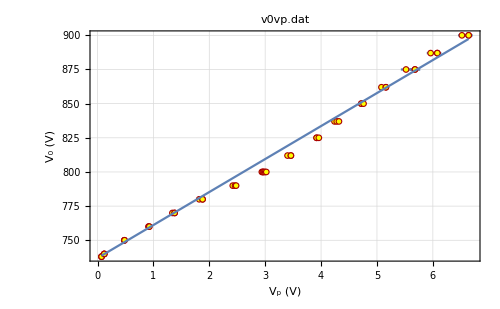
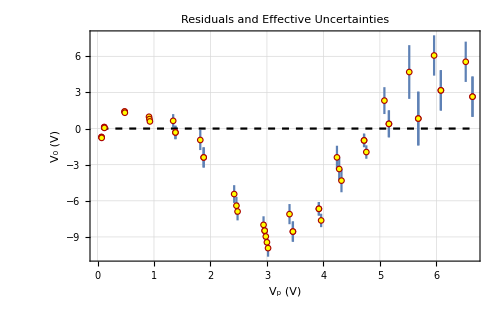
-Graphics-
-Graphics-
y(x) = a + b x
a= 
736.996 | b= 
24.15 | 
σ_a= 
0.0157803 | σ_b= 
0.0336788 | χ^2/(n-2)= 
100.683

```mathematica
LinearDifferencePlot[FrameLabel->{"V_p (V)","V_0 (V)"}]
```

We observe a relatively bad linear fit indicated by the large (χ̃)^2 and the clear trend in the residuals. As we calculated in the pre-lab, this indicates that some of our data points were taken with a V_0 for which the thin-sheath approximation does not hold, and therefore neither does our derived linear relation between V_p and V_0.

We have estimated the upper threshold for linear behavior to be around 800V, and this is indeed around where we observe a change in behavior. Therefore we remove the data points taken with V_0>800V and perform a linear fit again. We also remove the data points we used for the point-estimate of V_Th, as those were taken at very low signal-to-noise ratios and are prone to error. The small V_0 measurements do however show some loss of linearity in V_p against V_0, possibly just due to measurement error for the reason mentioned, but this may also be due to a defect in our model at low bias voltages.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 20/v0vp.dat

File comment header:

V0(V)	Vp(V)

LoadFile::sorted: Data sorted in increasing x order.

Read 51 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{755.3,803.5}

n= 18

33 points removed.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
LinearFit[]
```

n = 18

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
743.415 | b= 
19.0792 | 
σ_a= 
0.563846 | σ_b= 
0.252509 | Std. deviation= 
0.835833

Fit of (x±σ_x,y±σ_y)

a= 
742.113 | b= 
19.5905 | 
σ_a= 
0.161309 | σ_b= 
0.111408 | χ^2/(n-2)= 
3.16602

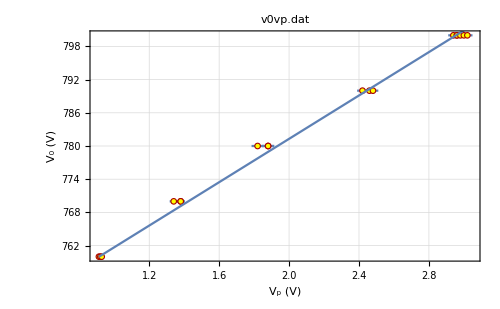
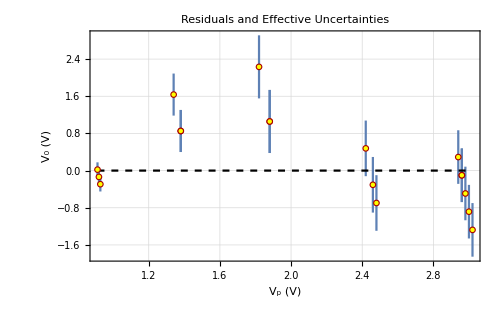
-Graphics-
-Graphics-
y(x) = a + b x
a= 
742.113 | b= 
19.5905 | 
σ_a= 
0.161309 | σ_b= 
0.111408 | χ^2/(n-2)= 
3.16602

```mathematica
LinearDifferencePlot[FrameLabel->{"V_p (V)","V_0 (V)"}]
```

As expected, we observe a much better fit as indicated by the relatively low (χ̃)^2. The residuals do appear to show a (much less discernible) trend, again possibly showing that a linear model is not quite adequate, but they are mostly within error and therefore should be perfectly fine to use for the following analysis.

From the y-intercept of our linear plot, we can estimate V_Th=742.1 ± 0.2V. We observe that this is relatively close to our in-lab point estimate of 738 V.

## Determining RC time constant in CI mode, τ

The long-term exponential decay of the Charge Integrated pulse is used to determine the RC time constant, τ, of the circuit in RC mode. We will then use τ to calculate C, the total capacitance of the circuit.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"Tek waveform files"->{"*.csv","*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadTekFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 20/Geiger Muller/800_exp_decay.csv

File comment header:

Record Length 2500 Points
Sample Interval 0.00002 s
Trigger Point 660.000013 Samples
Source CH1 
Vertical Units Volts 
Vertical Scale 0.499999989 
Vertical Offset 0 
Horizontal Units s 
Horizontal Scale 0.005 
Pt Fmt Y 
Yzero -3.28 
Probe Atten 10. 
Note TDS 1001B - 2:26:42 PM   5/3/2018

Read 2500 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.00032,0.01995}

n= 981

1519 points removed.

```mathematica
DecayingExponentialLFit::usage
```

DecayingExponentialLFit[ ] fits data with: 
y = a\ ⅇ^b\ x + c + d\ (x - xmin) 
Important: b must be negative (i.e. decaying exponential).  

Set the value of the variable:  region1 
to the x-location where the linear background becomes dominant before calling this function.  It must be true that: xmin < region1 < xmax.  

DecayingExponentialLFit[r1] sets region1 = r1 and then does the fit.

```mathematica
With[{x = SetX[ LogDataPlot[], Log -> False, Label -> "Set the X value for region1." ]}, 
  Print[x]; 

  DecayingExponentialLFit[x] 
]
```

0.004995

n = 981

y(x) = a Exp[b x] + c + d (x - x_min)

Fit of (x,y)  (unweighted)

a= 
3.0368 | b= 
-179.662 | c= 
-0.0126833 | d= 
0.560741 | x_min= 
0.00034
σ_a= 
0.00814618 | σ_b= 
0.656363 | σ_c= 
0.00894566 | σ_d= 
0.425192 | 
Std. deviation= 
0.00887417 |  |  |  |

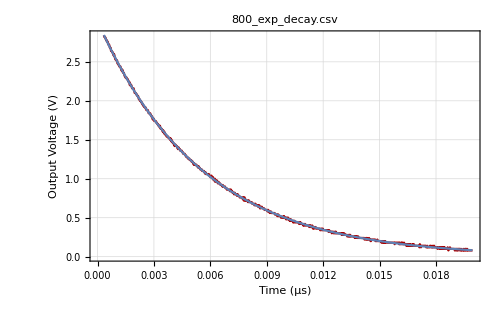
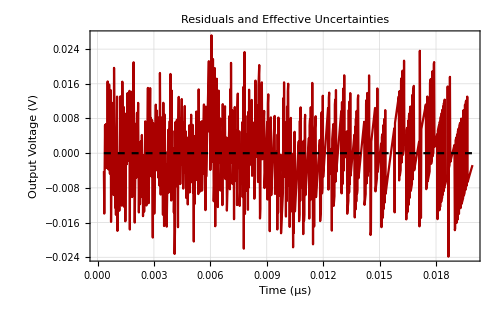
-Graphics-
-Graphics-
y(x) = a Exp[b x] + c + d (x - x_min)
a= 
3.0368 | b= 
-179.662 | c= 
-0.0126833 | d= 
0.560741 | x_min= 
0.00034
σ_a= 
0.00814618 | σ_b= 
0.656363 | σ_c= 
0.00894566 | σ_d= 
0.425192 | 
Std. deviation= 
0.00887417 |  |  |  |

```mathematica
LinearDifferencePlot[FrameLabel->{"Time (μs)","Output Voltage (V)"}]
```

```mathematica
τ=-1/b {1,(-Abs[sigb])/b}(* s *);
ScientificForm[τ,3]
```

{5.57×10^-3,2.03×10^-5}

```mathematica
cap=τ/(5*10^6) (* F *);
ScientificForm[cap,4]
```

{1.113×10^-9,4.067×10^-12}

We obtain a reasonable fit as far as we can tell by the amplitude and distribution of the residuals (we have a single decay curve and therefore cannot perform a goodness-of-fit test). This gives us an estimate of τ=5.56±0.02ms, from which we calculate C=τ/R=1.113±0.004 nF. Note that we have an underestimate on the uncertainty, as we do not know the tolerance of the 5MΩ resistance.

## Extracting relevant data from oscilloscope traces

### Helper functions to process data

```mathematica
(* We write a function to commit fit parameters to a list for each dataset. *)

(* Initialize list *)
fitParam={};

(* We will create a list with the structure {Subscript[V, 0],{{a, b, siga,  sigb # below Subscript[V, e]},{a, b, siga, sigb # above Subscript[V, e]}}}.
IMPORTANT: Need to start inputting values with parameters below Subscript[V, e], then above Subscript[V, e]. The reg argument can be either 'l' for below Subscript[V, e], or 'm' for above Subscript[V, e]. *)
addValues[v0_,reg_]:=Module[
{index},
If[
ToString[reg]=="l",
fitParam=Join[fitParam,{{v0,{{a,b,siga,sigb},{}}}}
],
If[
ToString[reg]=="m",
(index=Position[fitParam[[All,1]],v0][[1]][[1]];fitParam[[index]][[2]][[2]]={a,b,siga,sigb})
]
]
];

(* We also create a list for the Subscript[V, p] data. In order to find Subscript[V, p], we smooth the dataset to get rid of high-frequency electrical noise by performing a moving average, then select the maximum value. *)

(* Initialize list *)
vpVal={};

(* We create a list with structure {Subscript[V, 0],Subscript[V, p]} *)
vpValues[filename_,v0_]:=Module[
{data,dataAvg,maxIndex,max},
(
LoadTekFile[filename];
Pause[3];
SaveFile[StringReplace[filename,"csv"->"dat"]];
Pause[3];
data=Import[StringReplace[filename,"csv"->"dat"]];
dataAvg=MovingAverage[data[[All,2]],20];
Export[StringReplace["avg_%","%"->StringReplace[filename,"csv"->"dat"]],dataAvg];
maxIndex=Ordering[dataAvg,-1][[1]];
max=dataAvg[[maxIndex]];
vpVal=Join[vpVal,{{v0,max}}];
)
];
```

### Processing data for analysis

```mathematica
(* We use our functions to store the data we pull from the fits of long and short timescale data for different bias voltages. *)
```

```mathematica
(* We start with the Subscript[V, e] data, looping through the following commands for every dataset. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"Tek waveform files"->{"*.csv","*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadTekFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 20/Geiger Muller/760_short.csv

File comment header:

Record Length 2500 Points
Sample Interval 4.e-9 s
Trigger Point 870.000033 Samples
Source CH1 
Vertical Units Volts 
Vertical Scale 0.1 
Vertical Offset 0 
Horizontal Units s 
Horizontal Scale 1.e-6 
Pt Fmt Y 
Yzero -3.28 
Probe Atten 10. 
Note TDS 1001B - 2:15:01 PM   5/3/2018

Read 2500 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-8.42×10^-7,1.686×10^-6}

n= 632

1868 points removed.

```mathematica
LinearFit[]
```

n = 632

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.141634 | b= 
88711.2 | 
σ_a= 
0.000182662 | σ_b= 
216.681 | Std. deviation= 
0.00397537

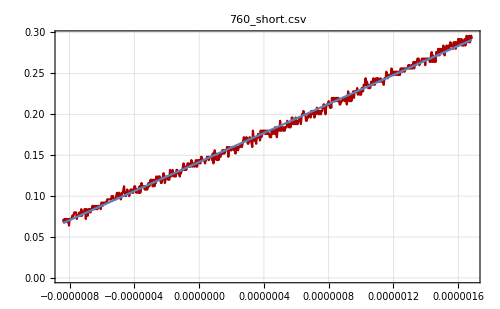
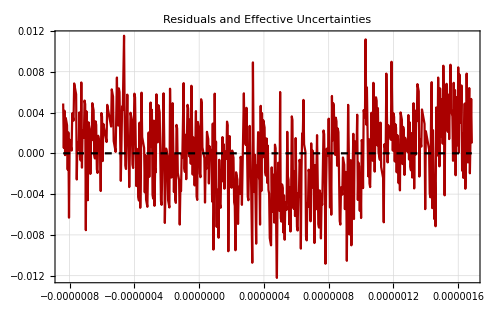
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.141634 | b= 
88711.2 | 
σ_a= 
0.000182662 | σ_b= 
216.681 | Std. deviation= 
0.00397537

```mathematica
LinearDifferencePlot[]
```

```mathematica
addValues[760,l]
```

{{760,{{0.141634,88711.2,0.000182662,216.681},{}}}}

```mathematica
fitParam
```

{{760,{{0.14211,87988.4,0.000164461,196.71},{0.197137,61789.1,0.00289608,1169.96}}},{770,{{0.148238,131204.,0.000222133,362.729},{0.263943,87402.8,0.00241459,959.95}}},{780,{{0.122872,200817.,0.00040219,532.662},{0.253494,138604.,0.00536139,2236.4}}}}

```mathematica
SetDirectory["Geiger Muller"]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 20/Geiger Muller

```mathematica
(* For safekeeping *)
Export["fitParam.dat",fitParam];
```

```mathematica
(* Now for the Subscript[V, p] data *)
```

```mathematica
files={{760,"760_long.csv"},{770,"770_long.csv"},{780,"780_long.csv"}};
vpValues[#[[2]],#[[1]]]&/@files
```

760_long.csv

File comment header:

Record Length 2500 Points
Sample Interval 2.e-7 s
Trigger Point 1020. Samples
Source CH1 
Vertical Units Volts 
Vertical Scale 0.20000001 
Vertical Offset 0 
Horizontal Units s 
Horizontal Scale 0.00005 
Pt Fmt Y 
Yzero -3.28 
Probe Atten 10. 
Note TDS 1001B - 2:03:34 PM   5/3/2018

Read 2500 data points.

Sorted data saved in 760_long.dat

770_long.csv

File comment header:

Record Length 2500 Points
Sample Interval 2.e-7 s
Trigger Point 1220. Samples
Source CH1 
Vertical Units Volts 
Vertical Scale 0.20000001 
Vertical Offset 0 
Horizontal Units s 
Horizontal Scale 0.00005 
Pt Fmt Y 
Yzero -3.28 
Probe Atten 10. 
Note TDS 1001B - 1:58:58 PM   5/3/2018

Read 2500 data points.

Sorted data saved in 770_long.dat

780_long.csv

File comment header:

Record Length 2500 Points
Sample Interval 2.e-7 s
Trigger Point 1213. Samples
Source CH1 
Vertical Units Volts 
Vertical Scale 0.499999989 
Vertical Offset 0 
Horizontal Units s 
Horizontal Scale 0.00005 
Pt Fmt Y 
Yzero -3.28 
Probe Atten 10. 
Note TDS 1001B - 2:11:25 PM   5/3/2018

Read 2500 data points.

Sorted data saved in 780_long.dat

{Null,Null,Null}

```mathematica
vpVal
```

{{760,0.9252},{770,1.3836},{780,1.902}}

```mathematica
(* For safekeeping *)
Export["vpVal.dat",vpVal];
```

### Extracting V_e , V_p and dV_out/dtdata from processed traces

```mathematica
(* We create a list with structure {Subscript[V, 0],Subscript[V, e],Subscript[σ, Subscript[V, e]]} by calutating Subscript[V, e] from our fit data and propagating uncertainties. We Flatten fitParam to make the uncertainty propagation more readable by avoiding messy indexing. *)
veInt=Partition[Flatten[fitParam],9];
veVal=Module[
{ve,a1, b1, siga1, sigb1,a2,b2,siga2,sigb2},
(
a1=2;b1=3;siga1=4;sigb1=5;a2=6;b2=7;siga2=8;sigb2=9;
Table[
{
veInt[[i]][[1]],ve=(veInt[[i]][[a1]]*veInt[[i]][[b2]]-veInt[[i]][[a2]]*veInt[[i]][[b1]])/(veInt[[i]][[b2]]-veInt[[i]][[b1]]),
ve*(Sqrt[(Sqrt[(veInt[[i]][[a1]]*veInt[[i]][[b2]](Sqrt[((veInt[[i]][[siga1]])/(veInt[[i]][[a1]]))^2+((veInt[[i]][[sigb2]])/(veInt[[i]][[b2]]))^2]))^2+(veInt[[i]][[a2]]*veInt[[i]][[b1]](Sqrt[((veInt[[i]][[siga2]])/(veInt[[i]][[a2]]))^2+((veInt[[i]][[sigb1]])/(veInt[[i]][[b1]]))^2]))^2]/(veInt[[i]][[a1]]*veInt[[i]][[b2]]-veInt[[i]][[a2]]*veInt[[i]][[b1]]))^2+(Sqrt[((veInt[[i]][[sigb2]])/(veInt[[i]][[b2]]))^2+((veInt[[i]][[sigb1]])/(veInt[[i]][[b1]]))^2])^2])
},
{i,1,Length[veInt]}
]
)
]
```

{{760,0.326914,0.0132689},{770,0.494825,0.00996239},{780,0.544507,0.0200946}}

```mathematica
(* We create a list with structure {Subscript[V, 0],dVout/dt,Subscript[σ, dVout/dt]}. *)
dvOut=Module[
{b2, sigb2},
(
b2=7;sigb2=9;
Table[
{veInt[[i]][[1]],veInt[[i]][[b2]],veInt[[i]][[sigb2]]},
{i,1,Length[veInt]}
]
)
]
```

{{760,61789.1,1169.96},{770,87402.8,959.95},{780,138604.,2236.4}}

```mathematica
(* We already have a list with structure {Subscript[V, 0],Subscript[V, p]}. We only have one sweep for each bias voltage and we did not obtain the peak value using a fit, therefore we do not have accurate, independent estimates for the uncertainty in Subscript[V, p]. To attempt a better error propagation in the following analysis, we simply observe the standard deviation of the fit for the exponential decay trace to be ~0.0089 V and use this as a somewhat arbitrary estimate of the uncertainty in our values for Subscript[V, p]. As mentioned *)
```

```mathematica
vpValUnc=Table[Flatten[{vpVal[[i]],0.0089}],{i,1,Length[vpVal]}]
```

{{760,0.9252,0.0089},{770,1.3836,0.0089},{780,1.902,0.0089}}

## Determining r_s0

We calculate r_s0 from our data and propagate uncertainties using r_s0=(a(b/a))^(V_e/V_p).

```mathematica
(* We define a function to calculate Subscript[r, s0] for each Subscript[V, 0] from the processed datasets above. *)
rs0[veUnc_,vpUnc_]:=
Module[
{aDim,bDim,rs0List},
(
aDim=0.3135*10^-3 (* m *);bDim=7.62*10^-3 (* m *);
rs0List=aDim(bDim/aDim)^(veUnc[[2]]/vpUnc[[2]]){1,Log[bDim/aDim] veUnc[[2]]/vpUnc[[2]] Sqrt[(veUnc[[3]]/veUnc[[2]])^2+(vpUnc[[3]]/vpUnc[[2]])^2]};
{vpUnc[[1]],rs0List[[1]],rs0List[[2]]}
)
]
```

```mathematica
rs0Val=Table[rs0[veVal[[i]],vpValUnc[[i]]],{i,1,Length[vpVal]}]
```

{{760,0.000967994,0.000045523},{770,0.000981341,0.0000236684},{780,0.000781524,0.0000265562}}

```mathematica
rs0Table=Join[{{"V_0(V)","r_s0 (10^-4m)"}},Table[{rs0Val[[i]][[1]],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[rs0Val[[i]][[2]]*10^4,3]],"%2"->ToString[NumberForm[rs0Val[[i]][[3]]*10^4,2]]}]},{i,1,Length[rs0Val]}]];
Grid[rs0Table,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

V_0(V) | r_s0 (10^-4m)
760 | 9.68 ± 0.46
770 | 9.81 ± 0.24
780 | 7.82 ± 0.27

```mathematica
Export["rs0Data.dat",rs0Val];
```

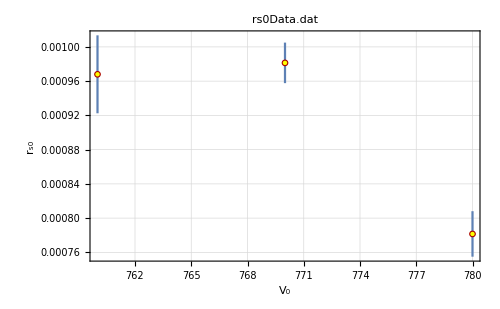

```mathematica
LinearDataPlot[FrameLabel->{"V_0","r_s0"}]
```

Because of the scarcity of the data, and the fact that we only have rough estimates on the uncertainties (since we only have a single trace for each data point), it is difficult to infer any sort of relation between V_0 and r_s0. Even disregarding those issues, we do not observe a clear trend in the table above or by plotting the three data points.

## Determining mobility of Ne^+

```mathematica
(* We use a package I wrote to help with propagation of uncertainties. *)
<<SimpleErrorPropagation`
```

```mathematica
errorFunction=PropagateUncertainties[(rsO Log[b/a])^2/(vP(vO-cp/cd(1/2 vP-vE)))dVOut,{rsO,vP,cp,vE,dVOut}]//Simplify
```

√((1.50903×10^25 cp^2 dVOut^2 rsO^4 sigmaVE^2 vP^2+1.50903×10^25 dVOut^2 rsO^4 sigmaCp^2 (vE-vP/2)^2 vP^2+102.011 rsO^4 sigmaDVOut^2 vP^2 (3.84615×10^11 cp vE+vO-1.92308×10^11 cp vP)^2+408.042 dVOut^2 rsO^2 sigmaRsO^2 vP^2 (3.84615×10^11 cp vE+vO-1.92308×10^11 cp vP)^2+1.50903×10^25 dVOut^2 rsO^4 sigmaVP^2 (1. cp vE+2.6×10^-12 vO-1. cp vP)^2)/(vP^4 (3.84615×10^11 cp vE+vO-1.92308×10^11 cp vP)^4))

```mathematica
μ[vO_,vP_,vE_,rsO_,cp_,dVOut_,sigmaVP_,sigmaVE_,sigmaRsO_,sigmaCp_,sigmaDVOut_]:={(rsO Log[b/a])^2/(vP(vO-cp/cd(1/2 vP-vE)))dVOut,√((1.5090314822808658*^25 cp^2 dVOut^2 rsO^4 sigmaVE^2 vP^2+1.5090314822808658*^25 dVOut^2 rsO^4 sigmaCp^2 (vE-vP/2)^2 vP^2+102.01052820218655 rsO^4 sigmaDVOut^2 vP^2 (3.846153846153846*^11 cp vE+vO-1.923076923076923*^11 cp vP)^2+408.0421128087462 dVOut^2 rsO^2 sigmaRsO^2 vP^2 (3.846153846153846*^11 cp vE+vO-1.923076923076923*^11 cp vP)^2+1.5090314822808658*^25 dVOut^2 rsO^4 sigmaVP^2 (1. cp vE+2.6000000000000002*^-12 vO-1. cp vP)^2)/(vP^4 (3.846153846153846*^11 cp vE+vO-1.923076923076923*^11 cp vP)^4))}
```

```mathematica
mobility=Partition[Flatten[Table[{vpValUnc[[i]][[1]],μn[vpValUnc[[i]][[1]] (* v0 *),vpValUnc[[i]][[2]] (* vp *), veVal[[i]][[2]] (* ve *),  rs0Val[[i]][[2]] (* rs0 *),cap[[1]] (* c *), dvOut[[i]][[2]] (* dvOut *),vpValUnc[[i]][[3]] (* sigmavp *), veVal[[i]][[3]] (* sigmave *),  rs0Val[[i]][[3]] (* sigmars0 *),cap[[2]] (* sigmacp *), dvOut[[i]][[3]] (* sigmadvOut *)]},{i,1,Length[vpValUnc]}]],3]
```

{{760,0.000900461,0.0000869232},{770,0.000896119,0.0000448031},{780,0.000741873,0.0000528969}}

```mathematica
mobilityTable=Join[{{"V_0(V)","μ_d (10^-4 m^2V^-1s^-1)"}},Table[{mobility[[i]][[1]],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[mobility[[i]][[2]]*10^4,3]],"%2"->ToString[NumberForm[mobility[[i]][[3]]*10^4,2]]}]},{i,1,Length[mobility]}]];
Grid[mobilityTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

V_0(V) | μ_d (10^-4 m^2V^-1s^-1)
760 | 9. ± 0.87
770 | 8.96 ± 0.45
780 | 7.42 ± 0.53

We now convert our mobility values to mobilities at standard pressure using the conversion factor determined in the pre-lab.

```mathematica
stdMobility=Table[{mobility[[i]][[1]],(mobility[[i]][[2]])/760*425,(mobility[[i]][[3]])/760*425},{i,1,Length[mobility]}]
```

{{760,0.000503547,0.0000486084},{770,0.000501119,0.0000250544},{780,0.000414863,0.0000295805}}

```mathematica
stdMobilityTable=Join[{{"V_0(V)","μ_d (10^-4 m^2V^-1s^-1)"}},Table[{stdMobility[[i]][[1]],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[stdMobility[[i]][[2]]*10^4,3]],"%2"->ToString[NumberForm[stdMobility[[i]][[3]]*10^4,2]]}]},{i,1,Length[stdMobility]}]];
Grid[stdMobilityTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

V_0(V) | μ_d (10^-4 m^2V^-1s^-1)
760 | 5.04 ± 0.49
770 | 5.01 ± 0.25
780 | 4.15 ± 0.3

We observe very similar mobilities for the bias voltages of 760V and 770V, both being higher than what we would expect for Ne^+ and lower than what we would expect for Br^+. This is somewhat expected for a mixture of ions with different mobilities, although we would need more information to better qualify this statement. The mobility for a bias voltage of 780V, however, appears to be very close to the expected mobility of Ne^+. Again, it is difficult to make any conclusive statements given the scarcity of the data.